# DysonTerms

Generates the nth term in the Dyson series expansion of a time dependent operator

## Definition

```mathematica
ClearAll[DysonTerms]
Options[DysonTerms]={"NumericIntegration"->False};

DysonTerms[n_,op_,opts:OptionsPattern[]]:=DysonTerms[n,op,NonCommutativeMultiply,0,opts];
DysonTerms[n_,op_,alg_,opts:OptionsPattern[]]:= DysonTerms[n,op,alg,0,opts]
DysonTerms[n_Integer?Positive, op_, alg_,t0_,OptionsPattern[]] := Module[{ts, integrand, limits,algebra},
    algebra=If[Head[alg]===NonCommutativeAlgebra,alg,NonCommutativeAlgebra@alg];
If[n == 1,
        Integrate[ op[Subscript[t, 1]], {Subscript[t, 1], 
            t0, T}]
        ,
        ts = Table[Subscript[t, i], {i, n}];
        integrand = algebra["Multiplication"] @@ Table[op[ts[[i]]], {i, n}];
        limits = Table[
            If[i == 1,
                {ts[[1]], t0, T}
                ,
                {ts[[i]], t0, ts[[i - 1]]}
            ]
            ,
            {i, 1, n}
        ];
If[TrueQ[OptionValue["NumericIntegration"]],Function[{T},If[NumericQ[T],NIntegrate[Evaluate@Simplify[integrand]/. T->T,Evaluate[Sequence@@(limits/. T->T)]],Null]],Integrate[FullSimplify[NonCommutativeExpand[integrand,algebra]],Sequence@@limits]
       ]
    ]
]
```

## Documentation

### Usage

DysonTerms[n,op]

generates the order-n term in the Dyson expansion of the operator op.

DysonTerms[n,op, alg]

generates the order-n term in the Dyson expansion of the operator op,  where alg specifies an algebraic "multiplicative" operation or a NonCommutativeAlgebra  (default is NonCommutativeMultiply).

DysonTerms[n,op, alg, t0]

generates the order-n term in the Dyson expansion of the operator op,  where alg specifies an algebraic "multiplicative" operation or a NonCommutativeAlgebra, and t0 is the initial integration time (default is 0).

DysonTerms[n, op,... ,"NumericIntegration"->False]

generates the order-n term in the Dyson expansion of the operator op,  the integrations are attempted numerically.

### Details & Options

The Dyson series expresses the time evolution operator 𝒰(t, t_0) for a time-dependent Hamiltonian H(t) as a time ordered exponential:
𝒰(t,t_0) =  𝒯 exp(-ⅈ/ℏ ∫_t_0^t H(t')ⅆt')

DysonTerms returns  the n-th  order term in the series expansion as D_n=𝒰^(n)(t, t_0)= (-ⅈ/h)^n ∫_t_0^t ⅆ t_1∫_t_0^t_1 ⅆ t_2... ∫_t_0^(t_(n-1)) ⅆ t_n  H(t_1)H(t_2)...H(t_n)  this construct enforces the time ordering (t >= t_1>= t_2... t_n>=t_0)

Useful for perturbative calculations in quantum mechanics, time-dependent perturbation theory, and quantum field theory

DysonTerms takes the following option

"NumericIntegration" | If set as True, it will return a function in terms of NIntegrate where the parameter is the upper limit. Otherwise it will do symbolic integration.
 By default, it is set as False.

## Examples

### Basic Examples

First order term D_1:

```mathematica
DysonTerms[1,A]
```

∫_0^T A[t_1]ⅆ t_1

Second order term D_2:

```mathematica
DysonTerms[2,A]
```

∫_0^T ∫_0^t_1 A[t_1]**A[t_2]ⅆ t_2ⅆ t_1

Second order term with Dot operation:

```mathematica
DysonTerms[2,B,Dot]
```

∫_0^T ∫_0^t_1 B[t_1].B[t_2]ⅆ t_2ⅆ t_1

Third order term D_3 , with lower integration limit equal to 1:

```mathematica
DysonTerms[3,B,NonCommutativeMultiply,1]
```

∫_1^T ∫_1^t_1 ∫_1^t_2 B[t_1]**B[t_2]**B[t_3]ⅆ t_3ⅆ t_2ⅆ t_1

### Scope

Dyson series up to third order for some generic operator in 2x2 Pauli algebra:

```mathematica
SymbolicIdentityArray[2]+Sum[(-ⅈ)^j DysonTerms[j,A,Dot],{j,3}]
```

-ⅈ ∫_0^T A[t_1]ⅆ t_1-∫_0^T ∫_0^t_1 A[t_1].A[t_2]ⅆ t_2ⅆ t_1+ⅈ ∫_0^T ∫_0^t_1 ∫_0^t_2 A[t_1].A[t_2].A[t_3]ⅆ t_3ⅆ t_2ⅆ t_1+2

Get the second order Dyson term for the particular time dependent operator  Δ/2 σ_z + A Cos(ω t) σ_x:

```mathematica
ClearAll[h4,Δ,ω,A,σ]
h4[t_]:=Δ/2 PauliMatrix[3]+A Cos[ω t] PauliMatrix[1]
```

```mathematica
DysonTerms[2,h4,Dot]
```

{{1/8 (T^2 Δ^2+(4 A^2 Sin[T ω]^2)/ω^2),-(A Δ (-2+2 Cos[T ω]+T ω Sin[T ω]))/(2 ω^2)},{(A Δ (-2+2 Cos[T ω]+T ω Sin[T ω]))/(2 ω^2),1/8 (T^2 Δ^2+(4 A^2 Sin[T ω]^2)/ω^2)}}

Consider a time dependent operator for fermionic algebra V(t)= α(t) ĉ+β(t)(ĉ)^† , where α and β are time dependent complex valued functions:

```mathematica
V[t_]:= α[t]c+β[t] SuperDagger[c]
```

Define the algebra:

```mathematica
alg = NonCommutativeAlgebra[<|"ScalarVariables"->Join[Flatten@Outer[#2[#1]&,{Subscript[t, 1],Subscript[t, 2]},{Identity,α,β}],{T}]|>];
```

Function for reducing fermionic algebra {c,c^†}=1, {c,c} = 0, {c^†,c^†} = 0:

```mathematica
reducer = NonCommutativePolynomialReduce[#,{Anticommutator[c,SuperDagger[c]]-1,c**c,SuperDagger[c]**SuperDagger[c]},{c,SuperDagger[c]},alg]&;
```

After simplification the identity and number operator n= c^†c terms remain, that depend on the integrals of the scalar functions:

```mathematica
(-ⅈ)^2 ReplaceAt[DysonTerms[2,V,alg],x_:>reducer[x][[-1]],1]
```

-∫_0^T ∫_0^t_1 (α[t_1] β[t_2]+c^†**c (α[t_2] β[t_1]-α[t_1] β[t_2]))ⅆ t_2ⅆ t_1

### Options

Define an operator in Pauli algebra:

```mathematica
ClearAll[h1];
h1[t_]:=Exp[-t^2] Cos[2t]PauliMatrix[2]+Sin[2t]PauliMatrix[3]
```

For second order term an exact expression could not be obtained or takes too long to integrate:

```mathematica
TimeConstrained[DysonTerms[2,h1,Dot],20]
```

$Aborted

Get a function to do numeric integration:

```mathematica
num = DysonTerms[2,h1,Dot,"NumericIntegration"->True];
```

Evaluate at some particular final time:

```mathematica
num[6.]
```

{{0.0561937,0.-0.150658 ⅈ},{0.-0.150658 ⅈ,0.0561937}}

### Applications

#### Driving field

Time dependent drive: V_I(t) =  g (ⅇ^(ⅈ ω t) a + ⅇ^(-ⅈ ω t) a^†)  for bosonic algebra:

```mathematica
Vi[t_]:=  g ( ⅇ^(ⅈ ω t)a+ⅇ^(-ⅈ ω t)SuperDagger[a])
```

Define algebra and a reduction function

```mathematica
alg = NonCommutativeAlgebra[<|"ScalarVariables"->{h,g,ω,Subscript[t, 1],Subscript[t, 2],T}|>];
reducer = NonCommutativePolynomialReduce[#,{a**SuperDagger[a]-SuperDagger[a]**a-1},{a,SuperDagger[a]},alg]&;
```

First order term:

```mathematica
-ⅈ DysonTerms[1,Vi,alg]
```

-(ⅇ^(-ⅈ T ω) (-1+ⅇ^(ⅈ T ω)) g (a ⅇ^(ⅈ T ω)+a^†))/ω

Second order term, simplified in normal order form:

```mathematica
reducer[(-ⅈ)^2 DysonTerms[2,Vi,alg]][[-1]]
```

(ⅈ g^2 (2 ⅈ-2 ⅈ ⅇ^(ⅈ T ω)-2 T ω))/(2 ω^2)+(ⅈ (2 ⅈ ⅇ^(ⅈ T ω)-ⅈ (1+ⅇ^(2 ⅈ T ω))) g^2 NonCommutativeMultiplya2**)/(2 ω^2)+(ⅇ^(-2 ⅈ T ω) (-1+ⅇ^(ⅈ T ω))^2 g^2 NonCommutativeMultiply(a^†)2**)/(2 ω^2)+((ⅈ g^2 (2 ⅈ-2 ⅈ ⅇ^(ⅈ T ω)-2 T ω))/(2 ω^2)+(ⅈ g^2 (2 ⅈ-2 ⅈ ⅇ^(-ⅈ T ω)+2 T ω))/(2 ω^2)) a^†**a

#### Chirped Gaussian Pulse

```mathematica
ClearAll[Ω0,τ,κ]
Hchirped[t_]:= 1/2 Ω0 ⅇ^(-t^2 / τ^2)(Cos[κ t^2]PauliMatrix[1]+Sin[κ t^2]PauliMatrix[2])
```

First order Dyson to QuantumOperator(using externally the Wolfram Quantum Framework):

```mathematica
dyson = {{-Graphics-, QuantumOperator}}[1+{{-Graphics-, QuantumOperator}}[-ⅈ DysonTerms[1,Hchirped,Dot,-3]],"Parameters"->{Ω0, τ, κ,T}];
```

```mathematica
dyson//TraditionalForm
```

00-((1/4+ⅈ/4) √(π/2) τ Ω0 (Erf[(3 (-1)^(1/4) √(-ⅈ+κ τ^2))/τ]+Erf[((-1)^(1/4) T √(-ⅈ+κ τ^2))/τ]))/(√(-ⅈ+κ τ^2))01-((1/4+ⅈ/4) √π τ Ω0 (Erfi[(3 (-1)^(1/4) √(ⅈ+κ τ^2))/τ]+Erfi[((-1)^(1/4) T √(ⅈ+κ τ^2))/τ]))/(√(2 ⅈ+2 κ τ^2))10+11

Hamiltonian in terms of QuantumOperator:

```mathematica
HchirpedOp = {{-Graphics-, QuantumOperator}}[1/2 Ω0 ⅇ^(-(t)^2 / τ^2)(Cos[κ t^2]{{-Graphics-, QuantumOperator}}["X"]+Sin[κ t^2]{{-Graphics-, QuantumOperator}}["Y"]),"Parameters"->{Ω0,τ,κ}];
```

First order approximation is good when this value is << 1:

```mathematica
dysonCondition[Ω0_,τ_,κ_]:= (Ω0 τ √π)/(2(1+κ^2 τ^4)^(1/4))
```

### Case Ω_0=1, τ = 1, τ = 10

Use QuantumEvolve and QuantumState for computing the evolution:

```mathematica
U ={{-Graphics-, QuantumEvolve}}[HchirpedOp[1.,1.,10.],None,{t,-3,3}];
ψ = U[{{-Graphics-, QuantumState}}["+"]];
```

Moderate agreement:

```mathematica
dysonCondition[1.,1.,10.]
```

0.279553

Plot the result from numerically solving the evolution:

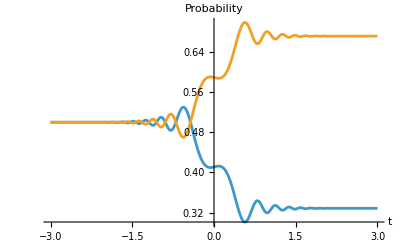

```mathematica
Plot[Evaluate@ψ[t]["ProbabilityList"],{t,-3,3},PlotRange->All,AxesLabel->{"t","Probability"},LabelStyle->13]
```

Plot result from Dyson:

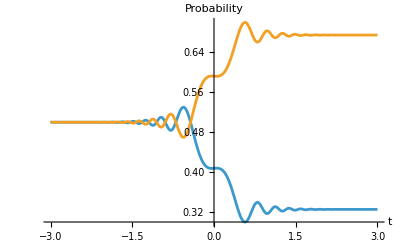

```mathematica
Plot[Evaluate[dyson[1.,1.,10.,t][{{-Graphics-, QuantumState}}["+"]]["Normalize"]["ProbabilityList"]],{t,-3,3},AxesLabel->{"t","Probability"},LabelStyle->13]
```

### Case Ω_0=25, τ = 30, τ = 15

Same procedure as the previous case (now we evolve the state |0⟩):

```mathematica
U ={{-Graphics-, QuantumEvolve}}[HchirpedOp[25.,30.,15.],None,{t,-3,3}];
ψ = U[{{-Graphics-, QuantumState}}["0"]];
```

There will not be  be good agreement for this case:

```mathematica
dysonCondition[25,30,15.]
```

5.72057

Plot the result from numerically solving the evolution:

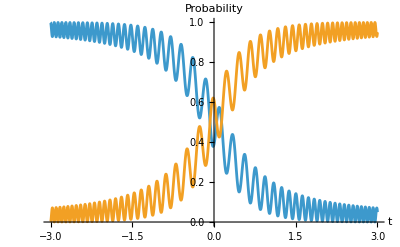

```mathematica
Plot[Evaluate@ψ[t]["ProbabilityList"],{t,-3,3},PlotRange->All,AxesLabel->{"t","Probability"},LabelStyle->13]
```

Plot result from Dyson :

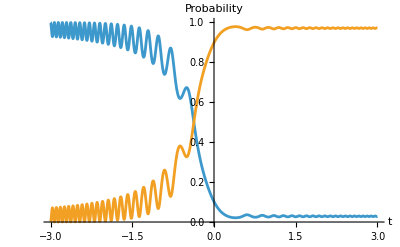

```mathematica
Plot[Evaluate[dyson[25.,30,15.,t][{{-Graphics-, QuantumState}}["0"]]["Normalize"]["ProbabilityList"]],{t,-3,3},PlotRange->{0,1},AxesLabel->{"t","Probability"},LabelStyle->13]
```

### Properties and Relations

#### Relation to Magnus expansion

### Possible Issues

If supplying an algebraic operation, has to be one compatible with NonCommutativeAlgebra:

```mathematica
DysonTerms[3,B,Times]
```

NonCommutativeAlgebra::ncalg: Times is not a valid NonCommutativeAlgebra specification.

NonCommutativeExpand::ncalg: NonCommutativeAlgebra[Times] is not a valid NonCommutativeAlgebra specification.

NonCommutativeAlgebra::ncalg: Times is not a valid NonCommutativeAlgebra specification.

NonCommutativeExpand::ncalg: NonCommutativeAlgebra[Times] is not a valid NonCommutativeAlgebra specification.

∫_0^T ∫_0^t_1 ∫_0^t_2 NonCommutativeExpand[NonCommutativeAlgebra[Times][Multiplication][B[t_1],B[t_2],B[t_3]],NonCommutativeAlgebra[Times]]ⅆ t_3ⅆ t_2ⅆ t_1

However it is possible to enforce a desired operation, defining a custom algebra:

```mathematica
alg = NonCommutativeAlgebra[<|"Multiplication"->Times|>];
DysonTerms[3,B,alg]
```

∫_0^T ∫_0^t_1 ∫_0^t_2 B[t_1] B[t_2] B[t_3]ⅆ t_3ⅆ t_2ⅆ t_1

### Neat Examples

## Source & Additional Information

### Contributed By

Bruno Tenorio

### Keywords

keyword 1

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

SymbolName (documented Wolfram Language symbol)

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Wolfram Quantum Framework

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

14.3+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.